# QKT Classic

## Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\Chaotic_eigenfunctions

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

```mathematica
Clear[F,Fun];

F[α_,k_,s_]:=Module[{a,sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}
];


Fun[α_,k_,s_]:=Module[{sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}.s
];

Clear[change];
change[s_]:=Module[{B=Sqrt[2/(1-s[[3]])]},
{s[[1]]*B,s[[2]]*B}
];

Clear[change2];
change2[Q_]:=Module[{B=Norm[Q]},
{Q[[1]]*Sqrt[1-(1/4)B^2],Q[[2]]*Sqrt[1-(1/4)B^2],(1/2)B^2 -1}
];

Clear[mapeo];
mapeo[Qini_,α_,k_,n_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Fun[α,k,#]&,s,n];
Map[change[#]&,list]
];

mapeob[Qini_,α_,k_,n_]:=Module[{map={},snew,a,s,Qnew},
AppendTo[map,Qini];
s=change2[Qini];
Do[
snew=MatrixPower[N[F[α,k,s]],2].s;
AppendTo[map,change[snew]];
s=snew;
,{l,1,n}];
map
];

Clear[Jx,Jy,Jz,M,mapeo1,jmas];
Jx[x_,y_,z_,α_,k_]:=x*Cos[α]-y*Sin[α]*Cos[k*x]+z*Sin[α]*Sin[k*x];
Jy[x_,y_,z_,α_,k_]:=x*Sin[α]+y*Cos[α]*Cos[k*x]-z*Cos[α]*Sin[k*x];
Jz[x_,y_,z_,α_,k_]:=y*Sin[k*x]+z*Cos[k*x];

M[Jini_,α_Real,k_Real]:=Module[{M},
M={{D[Jx[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},
{D[Jy[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},{D[Jz[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}}}//N;
M
];

mapeo1[si_,α_,k_,n_]:=Module[{s=si},
MatrixPower[F[α,k,s],n].s
];
```

## Energy surface

```mathematica
Clear[h2M,h2m];
(*h2M[α_,k_,Q_,P_]:=α((1/2)((Q-0.20)^2+P^2)-1)+(k*(Q-0.20)^2)(1-(1/4)((Q-0.20)^2+P^2));*)
h2M[α_,k_,Q_,P_]:=α((1/2)(Q^2+P^2)-1)+(k*Q^2)(1-(1/4)(Q^2+P^2));
```

```mathematica
Clear[α,k];
α=2.1;
k=100α;
Plot3D[h2M[α,k,Q,P],{Q,P}∈Disk[{0,0},1.999],PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["α = "<>ToString[α]<>", k = "<>ToString[k],23,Black],ColorFunction->"WatermelonColors",PlotLegends->Automatic]
```

```mathematica
Clear[α,k];
α=2.1;
k=-100α;
Plot3D[h2M[α,k,Q,P],{Q,P}∈Disk[{0,0},1.999],PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["α = "<>ToString[α]<>", k = "<>ToString[k],23,Black],ColorFunction->"WatermelonColors",PlotLegends->Automatic]
```

```mathematica
surface=ContourPlot[h2M[α,k,Q,P],{Q,P}∈Disk[{0,0},1.999],PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["α = "<>ToString[α]<>", k = "<>ToString[k],50,Black],Contours->100,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,ImageSize->600,GridLines->None,ColorFunction->"LightTerrain"]
```

```mathematica
surface=ContourPlot[h2M[α,k,Q,P],{Q,P}∈Disk[{0,0},1.999],PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["α = "<>ToString[α]<>", k = "<>ToString[k],50,Black],Contours->100,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,ImageSize->600,GridLines->None,ColorFunction->"LightTerrain"]
```

## Poincare differences

```mathematica
Clear[rot];
rot[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
```

```mathematica
Clear[α];
α=0.84;
τ=1;
```

```mathematica
randomregion=RandomPoint[Disk[{0.5,1},0.4],1000];
(*randomregion=Table[{i,0},{i,0,1.9990,0.0001}];*)
θ=-α/2;
(*randomregion=(rot[θ].#&/@randomregion);*)
randomregionb=-randomregion;
randomregion//Length
```

1000

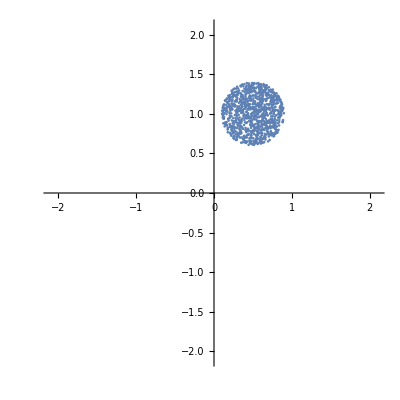

```mathematica
ListPlot[randomregion,AspectRatio->1,PlotRange->{{-2.1,2.1},{-2.1,2.1}}]
```

```mathematica
kicks=100;
k=100α;
puntosa=ParallelTable[Quiet[mapeo[i,α,k,kicks]],{i,randomregion}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregion]*(kicks+1),2}];
newpoincarea=(rot[θ].#&/@newpoincarea);
poincarec=Graphics[{PointSize[0.0025],Blue,Opacity[0.4],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[α*τ,45,Black],Style[", k = ",45,Black], Style[k,50,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->500];

puntosa=ParallelTable[Quiet[mapeo[i,α,k,kicks]],{i,randomregionb}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregion]*(kicks+1),2}];
newpoincarea=(rot[θ].#&/@newpoincarea);
poincarea=Graphics[{PointSize[0.0025],Black,Opacity[0.2],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[α*τ,45,Black],Style[", k = ",45,Black], Style[k,45,Black],Style[", n ="<>ToString[kicks],45,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->500];
```

```mathematica
Show[poincarea,poincarec,ImageSize->800,PlotRange->{{-2.1,2.1},{-2.1,2.1}}];
Export["poincare_alfa_"<>ToString[α]<>"_k_"<>ToString[k]<>"_kicks_"<>ToString[kicks]<>".png",Show[poincarea,poincarec,ImageSize->800,PlotRange->{{-2.1,2.1},{-2.1,2.1}}]];
```

# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\Chaotic_eigenfunctions

```mathematica
(*Operators*)
Clear[Sz,SM,Sm,Sx,Sy];
Sz[J_]:=DiagonalMatrix[Table[-J+k-1,{k,1,2J+1}]];
SM[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i+1)],{i,-J,J-1}],1];
Sm[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i-1)],{i,-J+1,J}],-1];
Sx[J_]:=(1/2)(SM[J]+Sm[J]);
Sy[J_]:=Sy[J]=(1/(2I))(SM[J]-Sm[J]);
Clear[Floq];
Floq[J_,α_,k_,τ_]:=N[MatrixExp[(-I*k/(2J))(Sx[J].Sx[J])].MatrixExp[(-I*α*τ)(Sz[J])]];
Clear[a2];
a2[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J,J}],20]]
];
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

# Method

```mathematica
Clear[haar];
haar[dim_Integer]:=Module[{l=2*dim+1,state1},
state1=Table[RandomReal[NormalDistribution[],2],{l}];
Normalize[state1[[All,1]]+I state1[[All,2]]]
];
```

```mathematica
radius=1.99999;
delta=0.03;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
boundaryPoints=(radius)Table[{Cos[i],Sin[i]},{i,0,2Pi,Pi/100}];
circlePoints=Select[gridPoints,Norm[#]<radius&];
region=Join[boundaryPoints,circlePoints];
region//Length
```

14153

```mathematica
ListPlot[region,AspectRatio->1];
```

```mathematica
Clear[J];
J=100;
α=0.84;
τ=1;
```

```mathematica
rotation=MatrixExp[I(N[Pi])Sx[J]];
rotation2=MatrixExp[I(N[α/2])Sz[J]];
rotation3=MatrixExp[I(N[-α/2])Sz[J]];
```

```mathematica
cohes=ParallelTable[Quiet[a2[J,i[[1]],i[[2]]]],{i,region}];
```

```mathematica
Clear[husimi];
husimi[ψ_]:=ParallelTable[{region[[i,1]],region[[i,2]],Abs[Conjugate[cohes[[i]]].ψ]^2},{i,Length[region]}]
```

```mathematica
0.84/0.42
```

2.

```mathematica
k=(0.42+10Pi);
(*mat=ConjugateTranspose[rotation2].Floq[J,α,k,τ].rotation2;*)
mat=ConjugateTranspose[rotation3].ConjugateTranspose[rotation].Floq[J,α,k,τ].rotation.rotation3;
matM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
eigenvalM=Eigenvalues[matM];
eigenvalm=Eigenvalues[matm];
matm=Table[mat[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
eigenvecM=Eigenvectors[matM];
eigenvecm=Eigenvectors[matm];
zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
```

```mathematica
data=husimi[neweigenvec[[2]]];
```

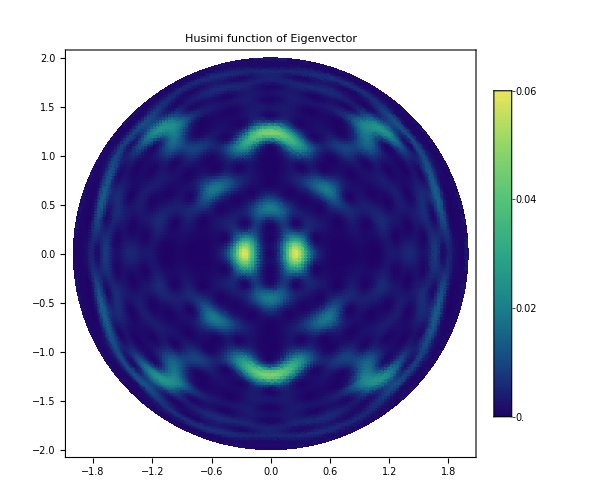

```mathematica
ListDensityPlot[data,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",ImageSize->500,PlotLabel->Style["Husimi function of Eigenvector",25,Black]]
```

```mathematica
d2=ParallelTable[Total[Abs[Conjugate[neweigenvec].i]^4],{i,cohes}];
```

```mathematica
newd2=Transpose[{region[[All,1]],region[[All,2]],-Log[d2]/Log[2J+1]}];
```

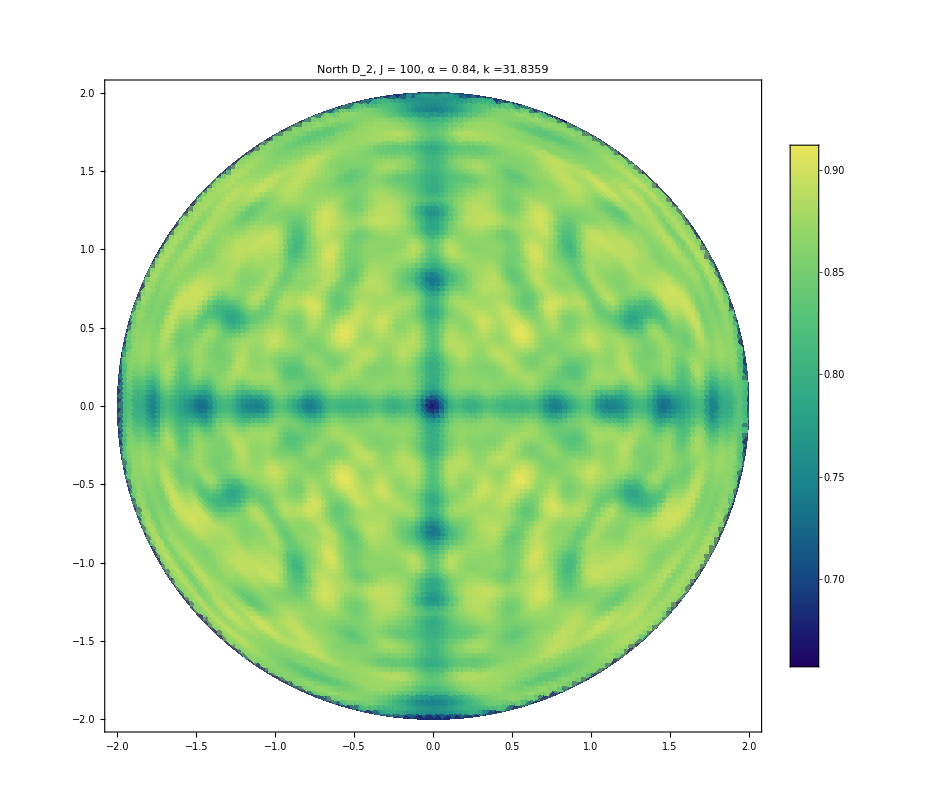

```mathematica
d2plotn=ListDensityPlot[newd2,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["North D_2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k],25,Black],ImageSize->800]
```

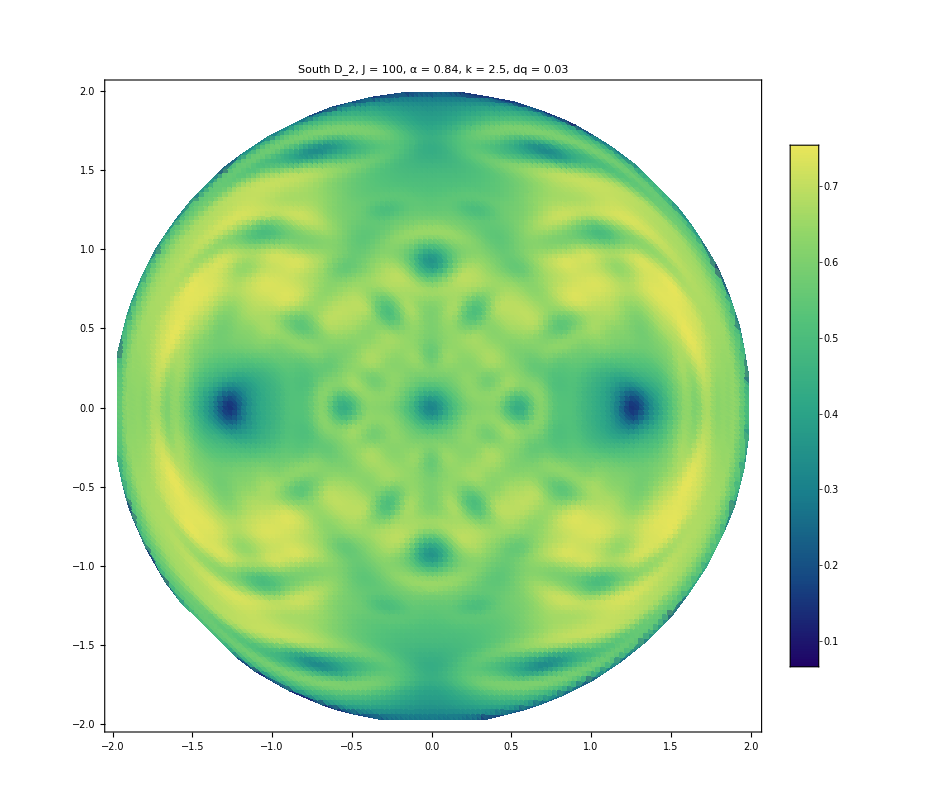

```mathematica
d2plots=ListDensityPlot[newd2,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["South D_2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta],25,Black],ImageSize->800]
```

```mathematica
Export["d2north_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>".png",d2plotn]
```

d2north_J_100_alpha_0.84_k_2.5.png

```mathematica
Export["d2south_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>"_dq_"<>ToString[delta]<>".png",d2plots]
```

d2south_J_100_alpha_0.84_k_2.5_dq_0.03.png

```mathematica
allhusimis=Table[husimi[i],{i,neweigenvec}];
newhusimis=Table[Transpose[{i[[All,1]],i[[All,2]],i[[All,3]]/Total[i[[All,3]]]}],{i,allhusimis}];
iprs=Table[Total[Abs[i[[All,3]]]^2],{i,newhusimis}];
```

```mathematica
sorted=Sort[iprs];
index=Table[Flatten[Position[iprs,sorted[[i]]]],{i,2J+1}];
sortedeigenvec=Table[neweigenvec[[i[[1]]]],{i,index}];
```

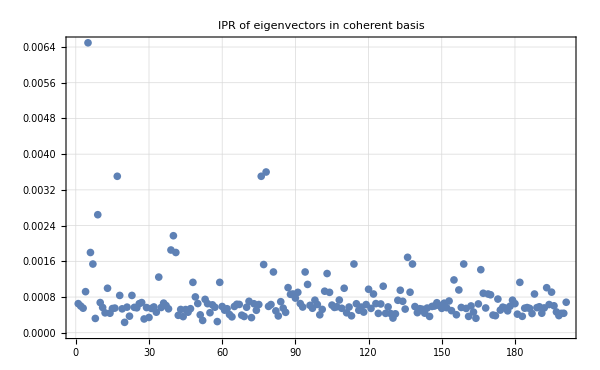

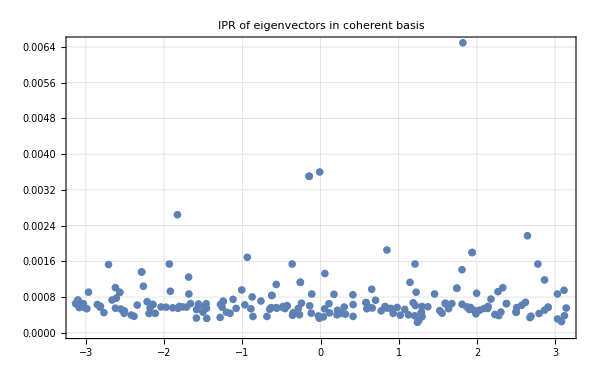

```mathematica
ListPlot[iprs,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["IPR of eigenvectors in coherent basis",25,Black],ImageSize->600]
ListPlot[Transpose[{Arg[neweigenval],iprs}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["IPR of eigenvectors in coherent basis",25,Black],ImageSize->600]
```

```mathematica
husi1=husimi[sortedeigenvec[[1]]];
husi2=husimi[sortedeigenvec[[-1]]];
```

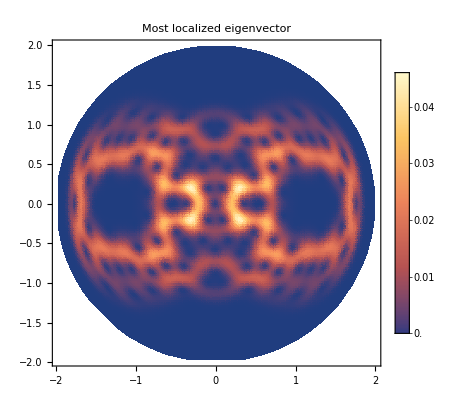

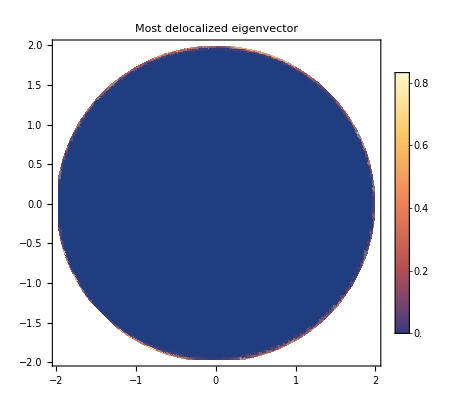

```mathematica
ListDensityPlot[husi1,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["Most localized eigenvector",25,Black]]
ListDensityPlot[husi2,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["Most delocalized eigenvector",25,Black]]
```

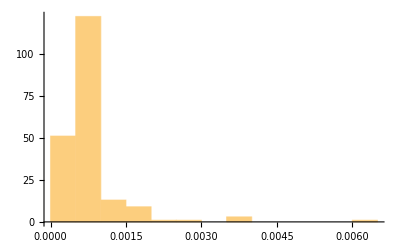

```mathematica
Histogram[iprs,15]
```

## Random states

```mathematica
random=Table[haar[100],{i,20}];
```

```mathematica
data=Table[husimi[i],{i,random}];
```

```mathematica
Table[ListDensityPlot[i,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",ImageSize->500,PlotLabel->Style["Husimi function of Eigenvector",25,Black]],{i,data}];
```

```mathematica
average=Mean[data];
```

```mathematica
average//Dimensions
```

{14153,3}

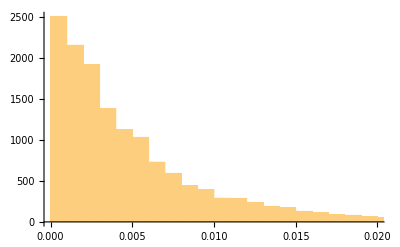
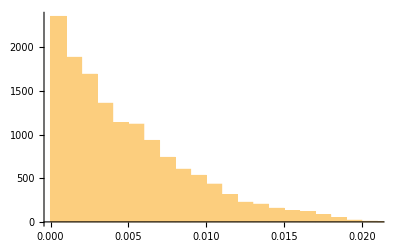
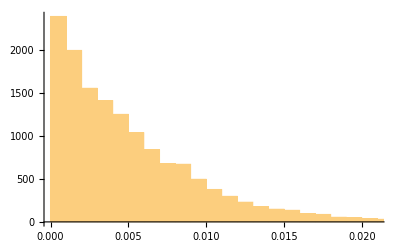
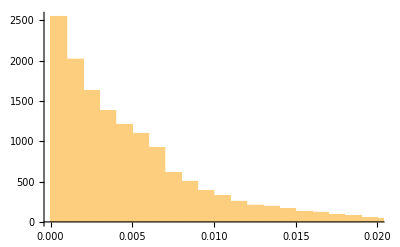
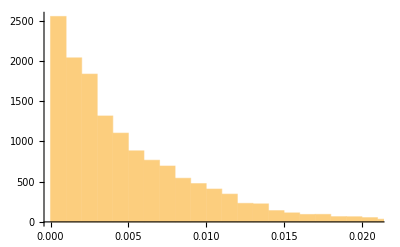
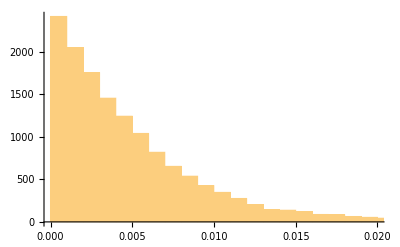
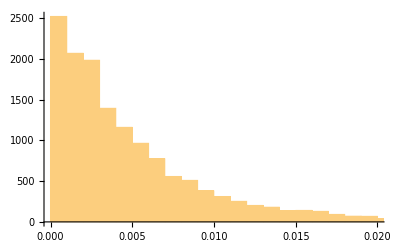
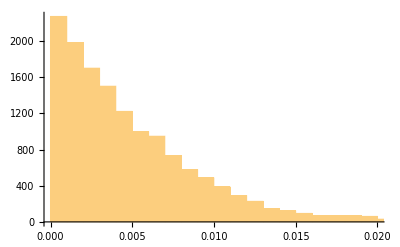

```mathematica
Table[Histogram[i[[All,3]]],{i,data}]
```

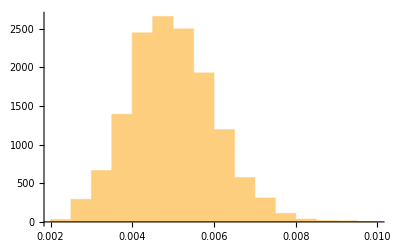

```mathematica
Histogram[average[[All,3]]]
```

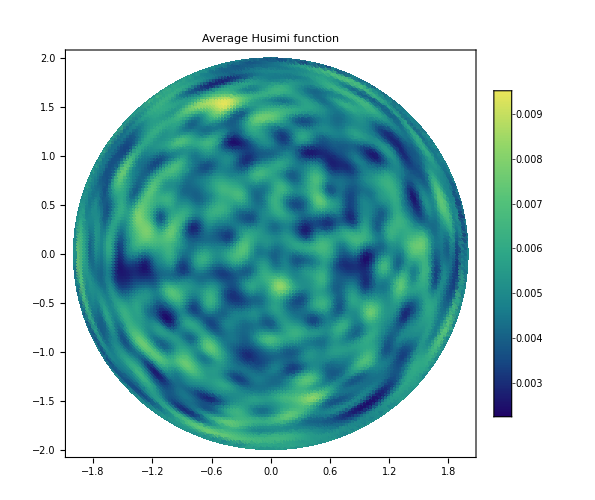

```mathematica
ListDensityPlot[average,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",ImageSize->500,PlotLabel->Style["Average Husimi function",25,Black]]
```

```mathematica
random1=haar[100];
random2=Normalize[Sum[RandomReal[]*i,{i,neweigenvec}]];
random3=Normalize[Sum[Exp[I*RandomReal[{-Pi,Pi}]]*RandomReal[]*i,{i,neweigenvec}]];
```

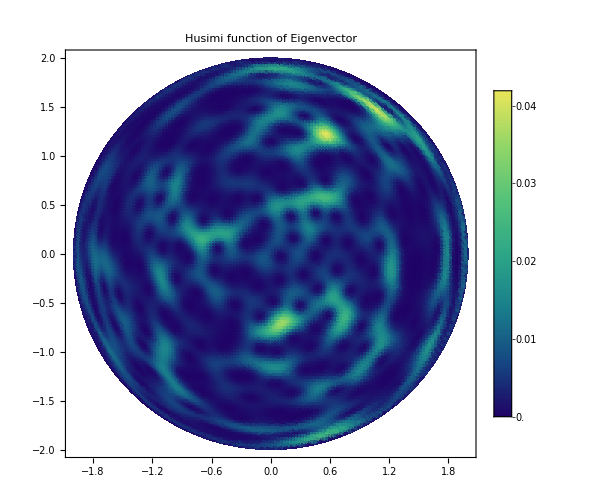

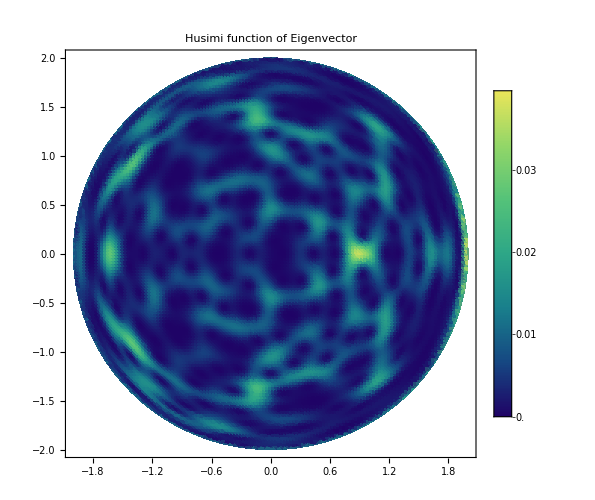

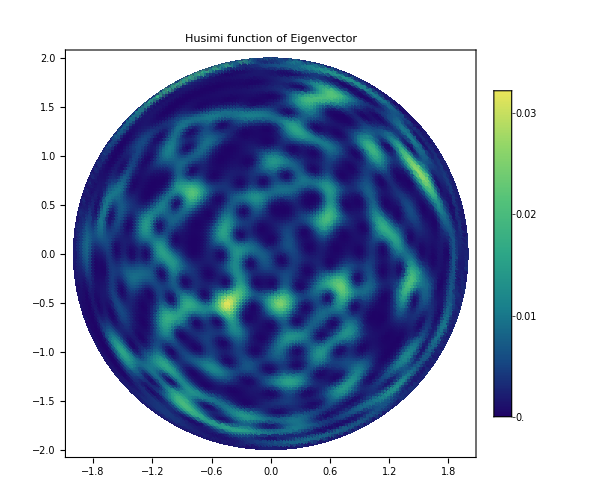

```mathematica
ListDensityPlot[husimi[random1],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",ImageSize->500,PlotLabel->Style["Husimi function of Eigenvector",25,Black]]
ListDensityPlot[husimi[random2],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",ImageSize->500,PlotLabel->Style["Husimi function of Eigenvector",25,Black]]
ListDensityPlot[husimi[random3],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",ImageSize->500,PlotLabel->Style["Husimi function of Eigenvector",25,Black]]
```

# Sorting Husimis

```mathematica
radius=1.99999;
delta=0.025;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
boundaryPoints=Select[gridPoints,Abs[Norm[#]^2-radius^2]<=2-1.99999&];
circlePoints=Select[gridPoints,Norm[#]<radius&];
region=Join[boundaryPoints,circlePoints];
```

```mathematica
Clear[J];
J=100;
α=2.1;
τ=1;
```

```mathematica
rotation=MatrixExp[I(N[Pi])Sx[J]];
rotation2=MatrixExp[I(N[α/2])Sz[J]];
rotation3=MatrixExp[I(N[-α/2])Sz[J]];
```

```mathematica
cohes=ParallelTable[Quiet[a2[J,i[[1]],i[[2]]]],{i,region}];
```

```mathematica
Clear[husimi];
husimi[ψ_]:=ParallelTable[{region[[i,1]],region[[i,2]],Abs[Conjugate[cohes[[i]]].ψ]^2},{i,Length[region]}]
```

```mathematica
k=100α;
matn=ConjugateTranspose[rotation2].Floq[J,α,k,τ].rotation2;
matM=Table[matn[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
matm=Table[matn[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
eigenvalM=Eigenvalues[matM];
eigenvalm=Eigenvalues[matm];
eigenvecM=Eigenvectors[matM];
eigenvecm=Eigenvectors[matm];
zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvecN=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];

mats=ConjugateTranspose[rotation3].ConjugateTranspose[rotation].Floq[J,α,k,τ].rotation.rotation3;
matM=Table[mats[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
matm=Table[mats[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
eigenvecM=Eigenvectors[matM];
eigenvecm=Eigenvectors[matm];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvecS=Riffle[neweigenvecM,neweigenvecm];
```

```mathematica
d2n=ParallelTable[Total[Abs[Conjugate[neweigenvecN].i]^4],{i,cohes}];
d2s=ParallelTable[Total[Abs[Conjugate[neweigenvecS].i]^4],{i,cohes}];
```

```mathematica
newd2n=Transpose[{region[[All,1]],region[[All,2]],-Log[d2n]/Log[2J+1]}];
newd2s=Transpose[{region[[All,1]],region[[All,2]],-Log[d2s]/Log[2J+1]}];
```

```mathematica
d2plotsn=ListDensityPlot[newd2n,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["North D_2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta],25,Black],ImageSize->1000];
d2plotss=ListDensityPlot[newd2s,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["South D_2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta],25,Black],ImageSize->1000];
```

```mathematica
Export["d2north_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>"_dq_"<>ToString[delta]<>".png",d2plotsn]
Export["d2south_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>"_dq_"<>ToString[delta]<>".png",d2plotss]
```

d2north_J_99_alpha_2.1_k_210._dq_0.025.png

d2south_J_99_alpha_2.1_k_210._dq_0.025.png

```mathematica
allhusimis=Table[husimi[i],{i,neweigenvecN}];
newhusimis=Table[Transpose[{i[[All,1]],i[[All,2]],i[[All,3]]/Total[i[[All,3]]]}],{i,allhusimis}];
iprs=Table[Total[Abs[i[[All,3]]]^2],{i,newhusimis}];
```

```mathematica
sorted=Sort[iprs];
index=Table[Flatten[Position[iprs,sorted[[i]]]],{i,2J+1}];
sortedeigenvecN=Table[neweigenvecN[[i[[1]]]],{i,index}];
```

```mathematica
plot1=ListPlot[Sort[iprs],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["IPR North, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k],25,Black],ImageSize->800,FrameLabel->{Style["i",20,Black],Style["IPR",20,Black]},Filling->Axis];
plot2=ListPlot[Transpose[{Arg[neweigenval],iprs}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["IPR North, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k],25,Black],ImageSize->800,FrameLabel->{Style["ϕ",20,Black],Style["IPR",20,Black]},Filling->Axis];
plot3=Histogram[iprs,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["IPR North, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k],25,Black],ImageSize->800,FrameLabel->{Style["i",20,Black],Style["IPR",20,Black]}];
```

```mathematica
Export["iprnortha_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>"_dq_"<>ToString[delta]<>".png",plot1]
Export["iprnorthb_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>"_dq_"<>ToString[delta]<>".png",plot2]
Export["iprnorthc_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>"_dq_"<>ToString[delta]<>".png",plot3]
```

iprnortha_J_99_alpha_2.1_k_210._dq_0.025.png

iprnorthb_J_99_alpha_2.1_k_210._dq_0.025.png

iprnorthc_J_99_alpha_2.1_k_210._dq_0.025.png

```mathematica
husi1=husimi[sortedeigenvecN[[1]]];
husi2=husimi[sortedeigenvecN[[-1]]];
```

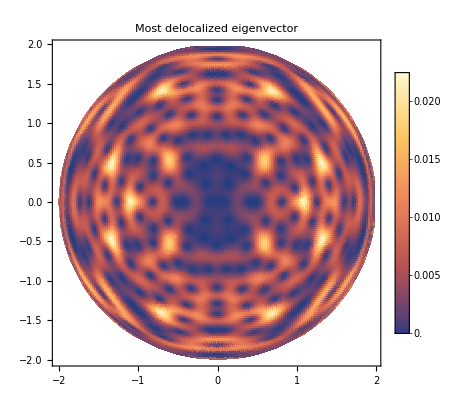

-Graphics-

```mathematica
ListDensityPlot[husi1,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["Most delocalized eigenvector",25,Black]]
ListDensityPlot[husi2,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["Most localized eigenvector",25,Black]]
```

```mathematica
allhusimissorted=Table[allhusimis[[i[[1]]]],{i,index}];
newhusimis=Table[Transpose[{i[[All,1]],i[[All,2]],i[[All,3]]/Total[i[[All,3]]]}],{i,allhusimissorted}];
```

```mathematica
ListDensityPlot[newhusimis[[1]],PlotRange->{All,All,{0,1}},PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North Eigenvec "<>ToString[1]<>", J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->800,ColorFunction->"BlueGreenYellow"]
ListDensityPlot[newhusimis[[-1]],PlotRange->{All,All,{0,1}},PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North Eigenvec "<>ToString[1]<>", J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->800,ColorFunction->"BlueGreenYellow"]
```

-Graphics-

-Graphics-

```mathematica
Do[

Export["northeigenvec_"<>ToString[i]<>"_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>"_dq_"<>ToString[delta]<>".png",ListDensityPlot[newhusimis[[i]],PlotRange->{All,All,{0,1}},PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North Eigenvec "<>ToString[i]<>", J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->1000,ColorFunction->"BlueGreenYellow"]]

,{i,2J+1}]
```

```mathematica
NotebookSave[]
```

## <H_0>

```mathematica
k=100α;
(*matn=ConjugateTranspose[rotation2].Floq[J,α,k,τ].rotation2;*)
matn=ConjugateTranspose[rotation2].MatrixPower[Floq[J,α,k,τ],3].rotation2;
matM=Table[matn[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
matm=Table[matn[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
eigenvalM=Eigenvalues[matM];
eigenvalm=Eigenvalues[matm];
eigenvecM=Eigenvectors[matM];
eigenvecm=Eigenvectors[matm];
zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvecN=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
```

```mathematica
ope=Sz[J];
```

```mathematica
jzs=ParallelTable[Chop[Conjugate[i].ope.i],{i,neweigenvecN}];
```

```mathematica
ListPlot[Sort[jzs/J],PlotRange->All,ImageSize->500]
```

-Graphics-

```mathematica
ListPlot[Sort[jzs/J],PlotRange->All,ImageSize->500]
```

-Graphics-

```mathematica
ListPlot[Transpose[{Arg[neweigenval],jzs/J}],PlotRange->All,ImageSize->600,PlotTheme->"Detailed"]
```

-Graphics-

```mathematica
ListPlot[Transpose[{Arg[neweigenval],jzs/J}],PlotRange->All,ImageSize->600,PlotTheme->"Detailed"]
```

-Graphics-

# Comparing similar k values

```mathematica
radius=1.99999;
delta=0.025;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
boundaryPoints=Select[gridPoints,Abs[Norm[#]^2-radius^2]<=2-1.99999&];
circlePoints=Select[gridPoints,Norm[#]<radius&];
region=Join[boundaryPoints,circlePoints];
```

```mathematica
Clear[J];
J=100;
α=0.84;
τ=1;
```

```mathematica
rotation=MatrixExp[I(N[Pi])Sx[J]];
rotation2=MatrixExp[I(N[α/2])Sz[J]];
rotation3=MatrixExp[I(N[-α/2])Sz[J]];
```

```mathematica
cohes=ParallelTable[Quiet[a2[J,i[[1]],i[[2]]]],{i,region}];
```

```mathematica
Clear[husimi];
husimi[ψ_]:=ParallelTable[{region[[i,1]],region[[i,2]],Abs[Conjugate[cohes[[i]]].ψ]^2},{i,Length[region]}]
```

```mathematica
k=100α;
```

```mathematica
klist=Sort[Table[100α+RandomReal[{-0.05,0.05}],{i,20}]]
```

{83.9536,83.956,83.9609,83.9675,83.9813,83.9816,83.9822,83.9824,83.9832,83.9919,83.9974,83.998,84.004,84.0158,84.0177,84.0215,84.0236,84.0373,84.0484,84.0497}

```mathematica
Do[

k=klist[[q]];
matn=ConjugateTranspose[rotation2].Floq[J,α,k,τ].rotation2;
matM=Table[matn[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
matm=Table[matn[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
eigenvalM=Eigenvalues[matM];
eigenvalm=Eigenvalues[matm];
eigenvecM=Eigenvectors[matM];
eigenvecm=Eigenvectors[matm];
zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvecN=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];

d2n=ParallelTable[Total[Abs[Conjugate[neweigenvecN].i]^4],{i,cohes}];
newd2n=Transpose[{region[[All,1]],region[[All,2]],-Log[d2n]/Log[2J+1]}];

d2plotsn=ListDensityPlot[newd2n,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["North D_2, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[klist[[q]]]<>", dq = "<>ToString[delta],25,Black],ImageSize->1000];
Export["d2north_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[klist[[q]]]<>"_dq_"<>ToString[delta]<>".png",d2plotsn];

allhusimis=Table[husimi[i],{i,neweigenvecN}];
newhusimis=Table[Transpose[{i[[All,1]],i[[All,2]],i[[All,3]]/Total[i[[All,3]]]}],{i,allhusimis}];
iprs=Table[Total[Abs[i[[All,3]]]^2],{i,newhusimis}];

sorted=Sort[iprs];
index=Table[Flatten[Position[iprs,sorted[[i]]]],{i,2J+1}];
sortedeigenvecN=Table[neweigenvecN[[i[[1]]]],{i,index}];

plot1=ListPlot[Sort[iprs],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["IPR North, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[klist[[q]]],25,Black],ImageSize->800,FrameLabel->{Style["i",20,Black],Style["IPR",20,Black]},Filling->Axis];
plot2=ListPlot[Transpose[{Arg[neweigenval],iprs}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["IPR North, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[klist[[q]]],25,Black],ImageSize->800,FrameLabel->{Style["ϕ",20,Black],Style["IPR",20,Black]},Filling->Axis];
plot3=Histogram[iprs,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["IPR North, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[klist[[q]]],25,Black],ImageSize->800,FrameLabel->{Style["i",20,Black],Style["IPR",20,Black]}];

Export["iprnortha_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[klist[[q]]]<>"_dq_"<>ToString[delta]<>".png",plot1];
Export["iprnorthb_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[klist[[q]]]<>"_dq_"<>ToString[delta]<>".png",plot2];
Export["iprnorthc_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[klist[[q]]]<>"_dq_"<>ToString[delta]<>".png",plot3];
allhusimissorted=Table[allhusimis[[i[[1]]]],{i,index}];
newhusimis=Table[Transpose[{i[[All,1]],i[[All,2]],i[[All,3]]/Total[i[[All,3]]]}],{i,allhusimissorted}];
Do[
Export["northeigenvec_"<>ToString[i]<>"_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[klist[[q]]]<>"_dq_"<>ToString[delta]<>".png",ListDensityPlot[newhusimis[[i]],PlotRange->{All,All,{0,1}},PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North Eigenvec "<>ToString[i]<>", J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->1000,ColorFunction->"BlueGreenYellow"]];
,{i,{1,-1}}];



,{q,Length[klist]}]
```